```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

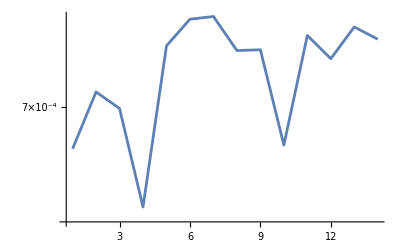

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
PlotRange->All,
Joined->True
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|Q5FFkG→-44.7703,Q4FFkG→-64.1257,Q3FFkG→148.033,PDrive_mean_x→-0.000181848,PDrive_mean_y→-1.2894×10^-6,PDrive_sigma_x→0.00021757,PDrive_sigma_y→0.000225994,PDrive_xCost→0.000283558,PDrive_yCost→0.000225998,PDrive_totalCost→0.000254778,PDrive_emitSI90_x→0.0000128861,PDrive_emitSI90_y→5.8939×10^-6,PDrive_zLen→0.0000192929,PDrive_zCentroid→980.591,PWitness_mean_x→-0.000179506,PWitness_mean_y→7.0073×10^-6,PWitness_sigma_x→0.000302995,PWitness_sigma_y→0.000189091,PWitness_xCost→0.000352177,PWitness_yCost→0.000189221,PWitness_totalCost→0.000270699,PWitness_emitSI90_x→0.0000533834,PWitness_emitSI90_y→3.8381×10^-6,PWitness_zLen→0.0000162455,PWitness_zCentroid→980.591,bunchSpacing→0.000209951,transverseCentroidOffset→8.6208×10^-6,maximizeMe→0.000822122|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

Q5FFkG : -44.7702905258
Q4FFkG : -64.1257015283
Q3FFkG : 148.0330987936
PDrive_mean_x : -0.0001818479
PDrive_mean_y : -1.2894e-6
PDrive_sigma_x : 0.00021757
PDrive_sigma_y : 0.0002259938
PDrive_xCost : 0.0002835584
PDrive_yCost : 0.0002259975
PDrive_totalCost : 0.0002547779
PDrive_emitSI90_x : 0.0000128861
PDrive_emitSI90_y : 5.8939e-6
PDrive_zLen : 0.0000192929
PDrive_zCentroid : 980.5912115356
PWitness_mean_x : -0.0001795064
PWitness_mean_y : 7.0073e-6
PWitness_sigma_x : 0.0003029953
PWitness_sigma_y : 0.0001890913
PWitness_xCost : 0.0003521771
PWitness_yCost : 0.0001892211
PWitness_totalCost : 0.0002706991
PWitness_emitSI90_x : 0.0000533834
PWitness_emitSI90_y : 3.8381e-6
PWitness_zLen : 0.0000162455
PWitness_zCentroid : 980.591421487
bunchSpacing : 0.0002099514
transverseCentroidOffset : 8.6208e-6
maximizeMe : 0.0008221215

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

8.62078×10^-6

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv